```mathematica
λ=10; (* Plots behavior not affected by choice of wavelength since we are averaging over [0,λ] *)
q=(2Pi)/λ;
β=1;

j[u_,δ_,x_]:=(e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2)((PolyLog[2,-Exp[-β(u-δ Sin[q x])]]-PolyLog[2,-Exp[β(u-δ Sin[q x])]])-NIntegrate[(PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]])/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]/NIntegrate[1/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]); (* current solution as a function of u=Subscript[μ, 0], δ=δμ, x=x' *)
Subscript[j, aec][u_,δ_]:=(e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2)(1/λ NIntegrate[PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]],{t,0,λ}]-NIntegrate[(PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]])/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]/NIntegrate[1/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]); (* acoustoelectric current obtained by averaging j, function of u=Subscript[μ, 0], δ=δμ *)

a[u_,δ_]:=NIntegrate[(PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]])/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]/NIntegrate[1/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]; (* a[Subscript[μ, 0],δμ] = <n-/n+>/<1/n+> *)
b[u_,δ_]:=1/λ NIntegrate[PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]],{t,0,λ}]; (* b[Subscript[μ, 0],δμ] = <n- > *)
c[u_,δ_]:=1/λ NIntegrate[(PolyLog[2,-Exp[-β(u-δ Sin[q t])]]-PolyLog[2,-Exp[β(u-δ Sin[q t])]])/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}]; (* c[Subscript[μ, 0],δμ] = <n-/n+> *)
d[u_,δ_]:=1/λ NIntegrate[1/(Log[1+Exp[β(u-δ Sin[q t])]]+Log[1+Exp[-β(u-δ Sin[q t])]]),{t,0,λ}] (* d[Subscript[μ, 0],δμ] = <1/n+> *)
```

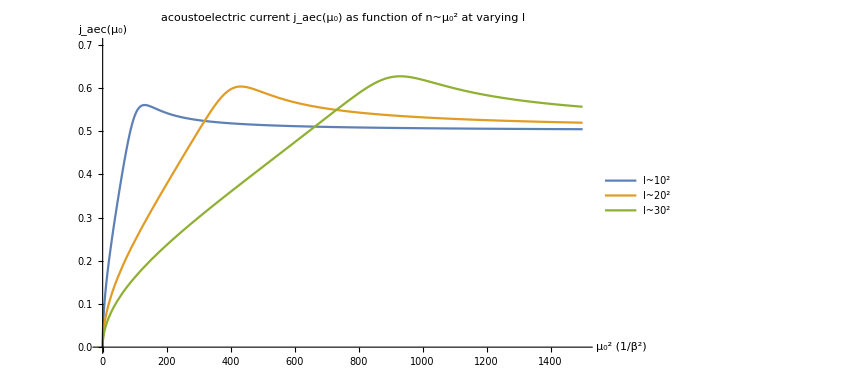

```mathematica
(* Plot[((e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2))^-1 j[30,30,x],{x,0,λ},PlotLabel->"current j(x') as function of relative position x' at fixed μ_0=50/β, δμ=30/β",Axes->True,AxesLabel->{"x'","j(x')"}](* plot of current j over a single wavelength for variable values of u=Subscript[μ, 0], δ=δμ *) *)
Plot[{1/10^2((e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2))^-1 Subscript[j, aec][u^(1/2),10],1/20^2((e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2))^-1 Subscript[j, aec][u^(1/2),20],1/30^2((e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2))^-1 Subscript[j, aec][u^(1/2),30]},{u,0,1500},PlotRange->{0,0.7},PlotLabel->"acoustoelectric current j_aec(μ_0) as function of n~μ_0^2 at varying I",Axes->True,AxesLabel->{"μ_0^2 (1/β^2)","j_aec(μ_0)"},PlotLegends->{"I~10^2","I~20^2","I~30^2"}] (* plot of acoustoelectric current <j> ove r a range of equilibrium chemical potentials u=Subscript[μ, 0], for variable values of δ=δμ *)
(* Plot[Evaluate[Table[1/δ^2((e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2))^-1 Subscript[j, aec][u^(1/2),30],{δ,15,40,5}]],{u,-2000,2000},PlotLabel->"acoustoelectric current j_aec(μ_0) as function of equilibrium chemical potential μ_0 (1/β) at fixed δμ=30/β",Axes->True,AxesLabel->{"μ_0 (1/β)","j_aec(μ_0)"}] (* plot of acoustoelectr *)ic current <j> ove r a range of equilibrium chemical potentials u=Subscript[μ, 0], for variable values of δ=δμ *)
```

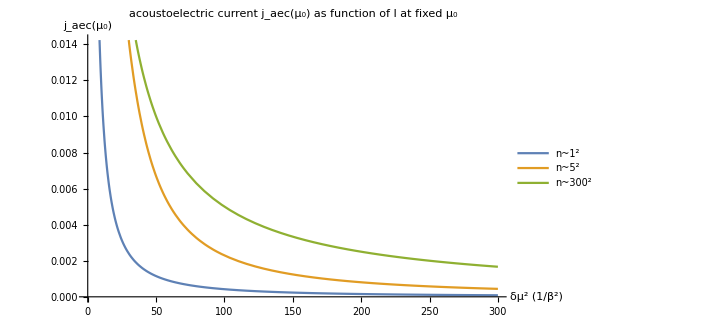

```mathematica
Plot[{1/δ^2((e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2))^-1 Subscript[j, aec][1,δ^(1/2)],1/δ^2((e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2))^-1 Subscript[j, aec][5,δ^(1/2)],1/δ^2((e Subscript[v, s])/(2Pi h^2 Subscript[v, F]^2 β^2))^-1 Subscript[j, aec][300,δ^(1/2)]},{δ,0,300},PlotLabel->"acoustoelectric current j_aec(μ_0) as function of I at fixed μ_0",Axes->True,AxesLabel->{"δμ^2 (1/β^2)","j_aec(μ_0)"},PlotLegends->{"n~1^2","n~5^2","n~300^2"}]
```

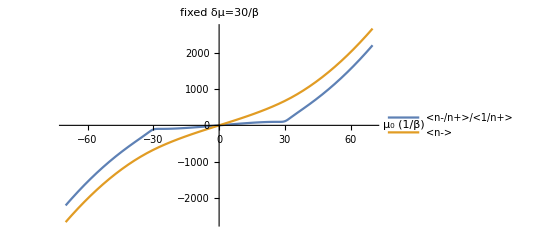

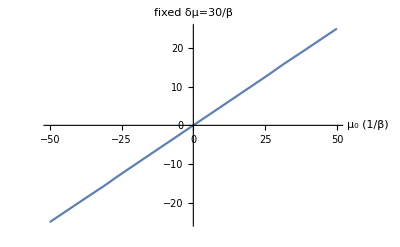

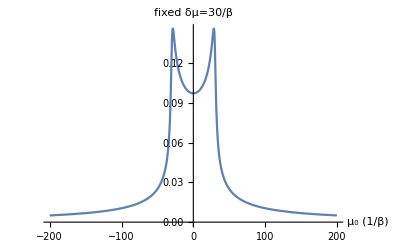

```mathematica
Plot[{a[u,30],b[u,30]},{u,-70,70},PlotLabel->"fixed δμ=30/β",PlotLegends->{"<n-/n+>/<1/n+>","<n->"},Axes->True,AxesLabel->{"μ_0 (1/β)",""}] (* plot of <n-/n+>/<1/n+> and <n- > over a range of equilibrium chemical potentials u=Subscript[μ, 0] *)
Plot[{c[u,30]},{u,-50,50},PlotLabel->"fixed δμ=30/β",PlotLegends->"<n-/n+>",Axes->True,AxesLabel->{"μ_0 (1/β)",""}] (* plot of <n-/n+> over a range of equilibrium chemical potentials u=Subscript[μ, 0] *)
Plot[{d[u,30]},{u,-200,200},PlotLabel->"fixed δμ=30/β",PlotLegends->"<1/n+>",Axes->True,AxesLabel->{"μ_0 (1/β)",""}] (* plot of <1/n+> over a range of equilibrium chemical potentials u=Subscript[μ, 0] *)
```

```mathematica
SubPlus[n](u_,δ_,x_):=((Subscript[m, 0] Subscript[v, F]^2)/(β Subscript[v, F]^2 h^2(2Pi)))^-1(Subscript[m, 0] Subscript[v, F]^2)/(β Subscript[v, F]^2 h^2(2Pi))(Log[1+E^(β (u-δ Sin[q x]))]+Log[1+E^(-β (u-δ Sin[q x]))]);
SubMinus[n](u_,δ_,x_):=(1/(β^2 Subscript[v, F]^2 h^2(2Pi)))^-1 1/(β^2 Subscript[v, F]^2 h^2(2Pi))(PolyLog[2,-E^(-β (u-δ Sin[q x]))]-PolyLog[2,-E^(β (u-δ Sin[q x]))]);
```